## Import and Export

```mathematica
1
```

```mathematica
Short[$ImportFormats,5]
```

{3DS,ACO,Affymetrix,AgilentMicroarray,AIFF,ApacheLog,ArcGRID,AU,AVI,Base64,BDF,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,CDED,«189»,VTK,WARC,WAV,Wave64,WDX,WebP,WLNet,WMLF,WXF,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XPORT,XYZ,ZIP}

```mathematica
2
```

```mathematica
Import["C:\\Users\\My-pc\\Desktop\\HelloWorld.txt"]
```

Hello World!

```mathematica
3
```

```mathematica
Import["C:\\Users\\My-pc\\Desktop\\HelloWorld.txt","Text"]
```

Hello World!

### Importing Files

```mathematica
4
```

```mathematica
Import["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv","CSV"]
```

{{id,grocery item,price,sold items,sales per day},{1,milk,4$,4,4 Jun 2019},{2,butter,3$,2,6 Jun 2019},{3,garlic,2$,1,7 Jun 2019},{4,apple,2$,4,1 Jun 2019},{5,orange,3$,5,8 Jun 2019},{6,orange juice,5$,2,8 Jun 2019},{7,cheese,5$,2,6 Jun 2019},{8,cookies,2$,5,9 Jun 2019},{9,grapes,4$,3,21 Jun 2019},{10,potatoe,2$,5,26 Jun 2019}}

```mathematica
5
```

```mathematica
Import["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv",{"Data",5;;10}]
```

{{4,apple,2$,4,1 Jun 2019},{5,orange,3$,5,8 Jun 2019},{6,orange juice,5$,2,8 Jun 2019},{7,cheese,5$,2,6 Jun 2019},{8,cookies,2$,5,9 Jun 2019},{9,grapes,4$,3,21 Jun 2019}}

```mathematica
6
```

```mathematica
Import["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv",{"Data",6,2}]
```

orange

```mathematica
7
```

```mathematica
Short[Import["C:\\Users\\My-pc\\Desktop\\Color_table.tsv","TSV"]] (*Rest,  to view the remain *)
```

{{number,color},{1,red},«7»,{9,magenta},{10,brown}}

```mathematica
8
```

```mathematica
Import["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv","CSV"];
Grid[%]
```

id | grocery item | price | sold items | sales per day
1 | milk | 4$ | 4 | 4 Jun 2019
2 | butter | 3$ | 2 | 6 Jun 2019
3 | garlic | 2$ | 1 | 7 Jun 2019
4 | apple | 2$ | 4 | 1 Jun 2019
5 | orange | 3$ | 5 | 8 Jun 2019
6 | orange juice | 5$ | 2 | 8 Jun 2019
7 | cheese | 5$ | 2 | 6 Jun 2019
8 | cookies | 2$ | 5 | 9 Jun 2019
9 | grapes | 4$ | 3 | 21 Jun 2019
10 | potatoe | 2$ | 5 | 26 Jun 2019

```mathematica
9
```

```mathematica
path="C:\\Users\\My-pc\\Desktop\\Grocery_List.xlsx";
Import[path,"Data"]
```

{{{id,grocery item, price, sold items},{1.,milk,4 $,4.},{2.,butter,3$,2.},{3.,garlic,2 $,1.},{4.,apple,2 $,4.},{5.,orange,3 $,5.},{6.,orange juice,5 $,2.},{7.,cheese,5 $,2.},{8.,cookies,2 $,5.},{9.,grapes,4 $,3.},{10.,potatoe,2 $,5.}}}

```mathematica
10
```

```mathematica
Import[path,#]&/@{"SheetCount","Sheets"}
```

```mathematica
{1,{Grocery_List}}
```

```mathematica
11
```

```mathematica
TableView[Import[path,{"Data",1},CharacterEncoding->"UTF-8"]]
```

idgrocery item price sold items1.milk4 $4.2.butter3$2.3.garlic2 $1.4.apple2 $4.5.orange3 $5.6.orange juice5 $2.7.cheese5 $2.8.cookies2 $5.9.grapes4 $3.10.potatoe2 $5.

```mathematica
12
```

```mathematica
file="C:\\Users\\My-pc\\Desktop\\Grocery_List_2.xlsx";
Import[file,{"Dataset",1},HeaderLines->1]
```

```mathematica
13
```

```mathematica
Import[file,{"Dataset",1},"EmptyField"->"NaN",HeaderLines->1]
```

```mathematica
14
```

```mathematica
Json=Import["C:\\Users\\My-pc\\Desktop\\Sports_cars.json","JSON"]
```

{{Model→Enzo Ferrari,Year→2002,Cylinders→12,Horsepower HP→660,Weight Kg→1255},{Model→Koenigsegg CCX,Year→2000,Cylinders→8,Horsepower HP→806,Weight Kg→1180},{Model→Pagani Zonda,Year→2002,Cylinders→12,Horsepower HP→558,Weight Kg→1250},{Model→McLaren Senna,Year→2019,Cylinders→8,Horsepower HP→800,Weight Kg→1309},{Model→McLaren 675 LT,Year→2015,Cylinders→8,Horsepower HP→675,Weight Kg→1230},{Model→Bugatti Veyron,Year→2006,Cylinders→16,Horsepower HP→1001,Weight Kg→1881},{Model→Audi R8 Spyder ,Year→2010,Cylinders→10,Horsepower HP→525,Weight Kg→1795},{Model→Aston Martin Vantage,Year→2009,Cylinders→8,Horsepower HP→926,Weight Kg→1705},{Model→Maserati Gran Turismo,Year→2010,Cylinders→8,Horsepower HP→405,Weight Kg→1955},{Model→Lamborghini Aventador S,Year→2017,Cylinders→12,Horsepower HP→740,Weight Kg→1740}}

```mathematica
15
```

```mathematica
Map[Association,Json,1]
```

{<|Model→Enzo Ferrari,Year→2002,Cylinders→12,Horsepower HP→660,Weight Kg→1255|>,<|Model→Koenigsegg CCX,Year→2000,Cylinders→8,Horsepower HP→806,Weight Kg→1180|>,<|Model→Pagani Zonda,Year→2002,Cylinders→12,Horsepower HP→558,Weight Kg→1250|>,<|Model→McLaren Senna,Year→2019,Cylinders→8,Horsepower HP→800,Weight Kg→1309|>,<|Model→McLaren 675 LT,Year→2015,Cylinders→8,Horsepower HP→675,Weight Kg→1230|>,<|Model→Bugatti Veyron,Year→2006,Cylinders→16,Horsepower HP→1001,Weight Kg→1881|>,<|Model→Audi R8 Spyder ,Year→2010,Cylinders→10,Horsepower HP→525,Weight Kg→1795|>,<|Model→Aston Martin Vantage,Year→2009,Cylinders→8,Horsepower HP→926,Weight Kg→1705|>,<|Model→Maserati Gran Turismo,Year→2010,Cylinders→8,Horsepower HP→405,Weight Kg→1955|>,<|Model→Lamborghini Aventador S,Year→2017,Cylinders→12,Horsepower HP→740,Weight Kg→1740|>}

```mathematica
16
```

```mathematica
Dataset[%]
```

```mathematica
17
```

```mathematica
Import["C:\\Users\\My-pc\\Desktop\\Sports_cars.json","RawJSON"]
```

{<|Model→Enzo Ferrari,Year→2002,Cylinders→12,Horsepower HP→660,Weight Kg→1255|>,<|Model→Koenigsegg CCX,Year→2000,Cylinders→8,Horsepower HP→806,Weight Kg→1180|>,<|Model→Pagani Zonda,Year→2002,Cylinders→12,Horsepower HP→558,Weight Kg→1250|>,<|Model→McLaren Senna,Year→2019,Cylinders→8,Horsepower HP→800,Weight Kg→1309|>,<|Model→McLaren 675 LT,Year→2015,Cylinders→8,Horsepower HP→675,Weight Kg→1230|>,<|Model→Bugatti Veyron,Year→2006,Cylinders→16,Horsepower HP→1001,Weight Kg→1881|>,<|Model→Audi R8 Spyder ,Year→2010,Cylinders→10,Horsepower HP→525,Weight Kg→1795|>,<|Model→Aston Martin Vantage,Year→2009,Cylinders→8,Horsepower HP→926,Weight Kg→1705|>,<|Model→Maserati Gran Turismo,Year→2010,Cylinders→8,Horsepower HP→405,Weight Kg→1955|>,<|Model→Lamborghini Aventador S,Year→2017,Cylinders→12,Horsepower HP→740,Weight Kg→1740|>}

```mathematica
18
```

```mathematica
Cars=Dataset[%];
```

```mathematica
19
```

```mathematica
Cars[SortBy[#Year& ]];
```

```mathematica
20
```

```mathematica
Short[Import["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt","HTML"]]
```

AC Antigua and Barbuda AE United Ara… Yemen ZA Zambia ZI Zimbabwe ZZ Ocean

```mathematica
21
```

```mathematica
Short[Import["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt","CSV"]]
```

{{AC Antigua and Barbuda},{AE United Arab Emirates},«216»,{ZZ Ocean}}

```mathematica
22
```

```mathematica
URLRead["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt"]
```

HTTPResponse[…]

```mathematica
23
```

```mathematica
URLDownload["https://www1.ncdc.noaa.gov/pub/data/igra/igra2-country-list.txt"]
```

```mathematica
File["C:\\Users\\lb-pc\\AppData\\Local\\Temp\\igra2-country-list-e4b630f3-7911-4720-acc9-a65b490d6e04.txt"]
```

### SemanticImport

```mathematica
24
```

```mathematica
SImprt=SemanticImport["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv"]
```

```mathematica
25
```

```mathematica
Quantity[2,"USDollars"]
```

2 $

```mathematica
26
```

```mathematica
Quantity[2,"USDollars"]//Head
```

Quantity

```mathematica
27
```

```mathematica
LinguisticAssistant
```

```mathematica
28
```

```mathematica
{QuantityMagnitude[Quantity[77, "Minutes"]],Head[%]}
```

{77,Integer}

```mathematica
29
```

```mathematica
QuantityUnit[Quantity[77, "Minutes"]]
```

Minutes

```mathematica
30
```

```mathematica
{Quantity[77, "Minutes"]-Quantity[77, "Minutes"],Quantity[77, "Minutes"]+Quantity[77, "Minutes"],Quantity[77, "Minutes"]*Quantity[77, "Minutes"],Quantity[77, "Minutes"]/Quantity[77, "Minutes"],Quantity[77, "Minutes"]*Quantity[3, "Meters"]}
```

{0 min,154 min,5929 min^2,1,231 m min}

```mathematica
31
```

```mathematica
SImprt[[All,"price"]]
```

```mathematica
32
```

```mathematica
Normal[%]
```

{4 $,3 $,2 $,2 $,3 $,5 $,5 $,2 $,4 $,2 $}

```mathematica
33
```

```mathematica
QuantityMagnitude[#]&[%]
```

{4,3,2,2,3,5,5,2,4,2}

```mathematica
34
```

```mathematica
SImprt[[All,{"id","sales per day"}]]
```

```mathematica
35
```

```mathematica
Normal[Values[%]]//InputForm
```

{{1, DateObject[{2019, 6, 4}, "Day", "Gregorian", -5.]}, 
 {2, DateObject[{2019, 6, 6}, "Day", "Gregorian", -5.]}, 
 {3, DateObject[{2019, 6, 7}, "Day", "Gregorian", -5.]}, 
 {4, DateObject[{2019, 6, 1}, "Day", "Gregorian", -5.]}, 
 {5, DateObject[{2019, 6, 8}, "Day", "Gregorian", -5.]}, 
 {6, DateObject[{2019, 6, 8}, "Day", "Gregorian", -5.]}, 
 {7, DateObject[{2019, 6, 6}, "Day", "Gregorian", -5.]}, 
 {8, DateObject[{2019, 6, 9}, "Day", "Gregorian", -5.]}, 
 {9, DateObject[{2019, 6, 21}, "Day", "Gregorian", -5.]}, 
 {10, DateObject[{2019, 6, 26}, "Day", "Gregorian", -5.]}}

```mathematica
36
```

```mathematica
Association[Apply[Rule,%,1]]//InputForm
```

<|1 -> DateObject[{2019, 6, 4}, "Day", "Gregorian", -5.], 
 2 -> DateObject[{2019, 6, 6}, "Day", "Gregorian", -5.], 
 3 -> DateObject[{2019, 6, 7}, "Day", "Gregorian", -5.], 
 4 -> DateObject[{2019, 6, 1}, "Day", "Gregorian", -5.], 
 5 -> DateObject[{2019, 6, 8}, "Day", "Gregorian", -5.], 
 6 -> DateObject[{2019, 6, 8}, "Day", "Gregorian", -5.], 
 7 -> DateObject[{2019, 6, 6}, "Day", "Gregorian", -5.], 
 8 -> DateObject[{2019, 6, 9}, "Day", "Gregorian", -5.], 
 9 -> DateObject[{2019, 6, 21}, "Day", "Gregorian", -5.], 
 10 -> DateObject[{2019, 6, 26}, "Day", "Gregorian", -5.]|>

```mathematica
37
```

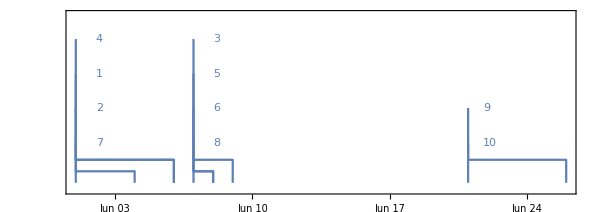

```mathematica
TimelinePlot[%]
```

```mathematica
38
```

```mathematica
SemanticImport["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv",{"Integer","String","Currency","Real", "Date"}]
```

```mathematica
39
```

```mathematica
SemanticImport["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv",Automatic,"Rows"][[1;;5]]//InputForm
```

{{1, "milk", Quantity[4, "USDollars"], 4, DateObject[{2019, 6, 4}, "Day", 
   "Gregorian", -5.]}, {2, "butter", Quantity[3, "USDollars"], 2, 
  DateObject[{2019, 6, 6}, "Day", "Gregorian", -5.]}, 
 {3, "garlic", Quantity[2, "USDollars"], 1, DateObject[{2019, 6, 7}, "Day", 
   "Gregorian", -5.]}, {4, "apple", Quantity[2, "USDollars"], 4, 
  DateObject[{2019, 6, 1}, "Day", "Gregorian", -5.]}, 
 {5, "orange", Quantity[3, "USDollars"], 5, DateObject[{2019, 6, 8}, "Day", 
   "Gregorian", -5.]}}

```mathematica
40
```

```mathematica
SemanticImport["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv",Automatic,"Columns"][[1;;2]]
```

{{1,2,3,4,5,6,7,8,9,10},{milk,butter,garlic,apple,orange,orange juice,cheese,cookies,grapes,potatoe}}

```mathematica
41
```

```mathematica
SemanticImport["C:\\Users\\My-pc\\Desktop\\Grocery_List.csv",ExcludedLines->{{10},{11}}]
```

### Export

```mathematica
42
```

```mathematica
Short[$ExportFormats,5]
```

{3DS,ACO,AIFF,AU,AVI,Base64,Binary,Bit,BMP,BSON,Byte,BYU,BZIP2,C,CDF,CDXML,Character16,Character32,Character8,CML,«148»,VRML,VTK,WAV,Wave64,WDX,WebP,WLNet,WMF,WMLF,WXF,X3D,XBM,XHTML,XHTMLMathML,XLS,XLSX,XML,XYZ,ZIP,ZPR}

```mathematica
43
```

```mathematica
Directory[]
```

```mathematica
"C:\\Users\\lb-pc\\Documents"
```

```mathematica
44
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
"C:\\Users\\My-pc\\Desktop"
```

```mathematica
45
```

```mathematica
Mydata=Table[Prime[i],{i,1,10}];
Export["New_File.txt",Mydata,"Table"]
Export["New_File.csv",Mydata]
```

New_File.txt

```mathematica
46
```

```mathematica
Export["C:\\Users\\My-pc\\Desktop\\New_File.TSV",Mydata,"TSV"]
```

```mathematica
"C:\\Users\\My-pc\\Desktop\\New_File.TSV"
```

```mathematica
47
```

```mathematica
SystemOpen["C:\\Users\\My-pc\\Desktop\\New_File.TSV"]
```

```mathematica
48
```

```mathematica
SystemOpen[NotebookDirectory[]]
```

```mathematica
49
```

```mathematica
TabD1=Table[i,{i,4}];TabD2=SetPrecision[Table[i/11,{i,4}],3];
```

```mathematica
50
```

```mathematica
Export["Tabular_data.xls",{{TabD1},{TabD2}}]
```

Tabular_data.xls

```mathematica
51
```

```mathematica
Export["Tabular_data_2.xls",{"Page number 1"->TabD1,"Page number 2"->TabD2}]
```

Tabular_data_2.xls

```mathematica
52
```

```mathematica
Export["New_data.xls",Transpose[{TabD1,TabD2}]]
```

New_data.xls

```mathematica
53
```

```mathematica
Grid[Transpose[{TabD1,TabD2}]]
```

1 | 0.0909
2 | 0.182
3 | 0.273
4 | 0.364

```mathematica
54
```

```mathematica
table1={{"Dog","Wolf"},{"Cat","Leopard"},{"Pigeon","Shark"}};
Export["Animal_table.xls",table1]
```

Animal_table.xls

```mathematica
55
```

```mathematica
NewD=Table[{i+j,i*j},{i,1,5},{j,1,5}];
Export["File_text.txt",NewD,"Text"]
Export["File_dat.dat",NewD,"Table"]
```

File_text.txt

File_dat.dat

```mathematica
56
```

```mathematica
Export["File_text.txt",NewD,"TSV"]
```

File_text.txt

```mathematica
57
```

```mathematica
{Export["File_csv.csv",NewD,"CSV"] ,
Export["File_tsv.tsv",NewD,"TSV"] }
```

{File_csv.csv,File_tsv.tsv}

```mathematica
58
```

```mathematica
Export["File_csv.csv",NewD,"CSV",TableHeadings->{"column 1","column 2" ,"column 3" ,"column 4","column 5"  }]
```

File_csv.csv

```mathematica
59
```

```mathematica
Labels={"Coordindates 1","Coordinates 2","Coordindates 3","Coordinates 4","Coordindates 5"};
Export["File_csv.csv",NewD,"CSV",TableHeadings->Labels]
```

File_csv.csv

```mathematica
60
```

```mathematica
SpData=ExampleData[{"Statistics","CarStoppingDistances"}]
```

{{4,2},{4,10},{7,4},{7,22},{8,16},{9,10},{10,18},{10,26},{10,34},{11,17},{11,28},{12,14},{12,20},{12,24},{12,28},{13,26},{13,34},{13,34},{13,46},{14,26},{14,36},{14,60},{14,80},{15,20},{15,26},{15,54},{16,32},{16,40},{17,32},{17,40},{17,50},{18,42},{18,56},{18,76},{18,84},{19,36},{19,46},{19,68},{20,32},{20,48},{20,52},{20,56},{20,64},{22,66},{23,54},{24,70},{24,92},{24,93},{24,120},{25,85}}

```mathematica
61
```

```mathematica
ExampleData[{"Statistics","CarStoppingDistances"},#]&/@{"Description","ColumnDescriptions"}
```

{Car stopping distances as a function of speed.,{Speed in miles per hour.,Stopping distance in feet.}}

```mathematica
62
```

```mathematica
SpDataset=Dataset[SpData,Background->LightBlue][All,<|#1->1,#2->2|>]&["Speed in miles per hours","Stopping distance in feet"]
```

```mathematica
63
```

```mathematica
Export["Dataset_csv.csv",SpDataset,"CSV"]
```

Dataset_csv.csv

```mathematica
64
```

```mathematica
Export["Dataset_tsv.tsv",SpDataset,"TSV"]
```

Dataset_tsv.tsv

```mathematica
65
```

```mathematica
Values@Normal@SpDataset
```

{{4,2},{4,10},{7,4},{7,22},{8,16},{9,10},{10,18},{10,26},{10,34},{11,17},{11,28},{12,14},{12,20},{12,24},{12,28},{13,26},{13,34},{13,34},{13,46},{14,26},{14,36},{14,60},{14,80},{15,20},{15,26},{15,54},{16,32},{16,40},{17,32},{17,40},{17,50},{18,42},{18,56},{18,76},{18,84},{19,36},{19,46},{19,68},{20,32},{20,48},{20,52},{20,56},{20,64},{22,66},{23,54},{24,70},{24,92},{24,93},{24,120},{25,85}}

```mathematica
66
```

```mathematica
ColTitles={"Speed in miles per hours","Stopping distance in feet"};
```

```mathematica
67
```

```mathematica
Short[ExprtData=Prepend[%%,ColTitles],1]
```

{{Speed in miles per hours,Stopping distance in feet},{4,2},{4,10},{7,4},{7,22},{8,16},«39»,{23,54},{24,70},{24,92},{24,93},{24,120},{25,85}}

```mathematica
68
```

```mathematica
Export["Stopping_distance_Dataset.xlsx",ExprtData,"XLSX"]
```

Stopping_distance_Dataset.xlsx

```mathematica
69
```

```mathematica
Association@
{
"Name"->"Ellis",
"Date of birth"->"1990,01,04",
"Height"->"180 cm",
"Favorite color"->"Red",
"Hobbies"->"Soccer, Pc gaming, Board games",
"Social netwoks"->"Twitter, Facebook"
};
Export["File_json.json",%,"JSON"]
```

File_json.json

```mathematica
70
```

```mathematica
Association@
{
"Name"->"Ellis",
"Date of birth"->DateObject[{1990,01,04}],
"Height"->Quantity[180,"Centimeters"],
"Favorite color"->"Red",
"Hobbies"->"Soccer, Pc gaming, Board games",
"Social netwoks"->"Twitter, Facebook"
};
User=Dataset[%]
```

```mathematica
71
```

```mathematica
Export["Dataset_json.json",User,"JSON"]
```

Dataset_json.json

```mathematica
72
```

```mathematica
Assoc1=<|"Log in Date"->DateObject[{2020,06,29}],"User ID"->123,"Status"->"Active"|>;Assoc2=<|"Log in Date"->DateObject[{2020,06,28}],"User ID"->122,"Status"->"Not Active"|>;
Dataset[{Assoc1,Assoc2}]
Export["Dataset2_json.json",%,"JSON"]
```

Dataset2_json.json

```mathematica
73
```

```mathematica
Assoc3="Player A"->Association["Date"->DateObject[{2020,06,29}],"User ID"->123,"Status"->"Active"];Assoc4="Player B"->Association["Date"->DateObject[{2020,06,28}],"User ID"->122,"Status"->"Not Active"];
Dataset[{<|Assoc3,Assoc4|>}]
```

```mathematica
74
```

```mathematica
Export["Dataset3_json.json",%,"JSON"]
```

Dataset3_json.json

```mathematica
75
```

```mathematica
Rules={"apple"->3,"car"->"3","2"->2};
Export["Rules.json",Rules,"JSON"]
```

Rules.json

```mathematica
76
```

```mathematica
Arry=Array[{#1,#2}&,{4,4}]
Export["Array.json",Arry,"JSON"]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}},{{4,1},{4,2},{4,3},{4,4}}}

Array.json

```mathematica
77
```

```mathematica
Association@
{
"Name"->"Ellis",
"Date of birth"->DateObject[{1990,01,04}],
"Height"->Quantity[180,"Centimeters"],
"Favorite color"->"Red",
"Hobbies"->"Soccer, Pc gaming, Board games",
"Social netwoks"->"Twitter, Facebook"
};
User=Dataset[%];
JsonFile=Export["Dataset_json_2.json",User,"JSON"];
```

```mathematica
78
```

```mathematica
AbsoluteFileName[JsonFile]
```

```mathematica
"C:\\Users\\My-pc\\Documents\\Dataset_json_2.json"
```

```mathematica
79
```

```mathematica
File[%]
```

```mathematica
File["C:\\Users\\My-pc\\Documents\\Dataset_json_2.json"]
```

```mathematica
80
```

```mathematica
ContentObject[%]
```

ContentObject[…]

```mathematica
81
```

```mathematica
ContentObject[%%]["Properties"]
```

{Location,FileName,ModificationDate,CreationDate,FileByteCount,FileExtension,Title,Plaintext}

### Searching Files with Wolfram language

```mathematica
82
```

```mathematica
NotebookDirectory[]
```

```mathematica
"C:\\Users\\My-pc\\Desktop\\"
```

```mathematica
83
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
"C:\\Users\\My-pc\\Desktop"
```

```mathematica
84
```

```mathematica
FileNames[]
```

{Color_table.txt,Grocery_List.csv,Hello_World,Hello_World.txt,import export.nb,weather.csv}

```mathematica
85
```

```mathematica
FindFile["Color_table.txt"]
```

```mathematica
"C:\\Users\\My-pc\\Desktop\\Color_table.txt"
```

```mathematica
86
```

```mathematica
FileNames["*.txt"]
```

{Color_table.txt,Hello_World.txt}